# Quantum Teleportation

Here we demonstrate the quantum teleportation using the Q3 Application.

QuissoCircuit | Circuit representation of elementary gates
Matrix | Converts QuissoCircuit and operator (or Ket) expressions to the matrix representation in the standard basis.
QuissoExpression | Converts the matrix representation to operator expressions

Function examining the quantum teleportation protocol.

Start with loading the package

```mathematica
<<Q3`Quisso`
```

Choose the symbol to denote the Qubitspaclet:Q3/ref/Qubits.

```mathematica
Let[Qubit,S]
```

Bob chooses randomly the state to teleport to Alice, and prepare the third Qubitpaclet:Q3/ref/Qubit Spaclet:Global/ref/S[3,Nonepaclet:ref/None] in it.

```mathematica
in=Basis[S[3]].Normalize@RandomReal[{-1,1},2]
```

0.265599 ␣+0.964083 1_S_3

Check the normalization of the state.

```mathematica
Dagger[in]**in//Chop
```

1.

Here is the quantum circuit of teleportation.

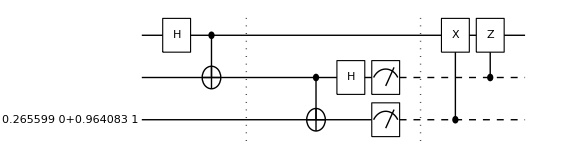

```mathematica
qc=QuissoCircuit[
in,LogicalForm[Ket[],S@{1,2}],
S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",
CNOT[S[2],S[3]],
S[2,6],{Measure[S[2]],Measure[S[3]]},"Separator",
ControlledU[S[3],S[1,1]],
ControlledU[S[2],S[1,3]]
]
```

Convert the quantum circuit (represented by QuissoCircuitpaclet:Q3/ref/QuissoCircuit) to Quisso expression by means of either QuissoExpresssionpaclet:Q3/ref/QuissoExpresssion or Matrixpaclet:Q3/ref/Matrix (usually faster).

```mathematica
outAll=QuissoExpression[qc]//Simplify
```

0.964083 1_S_11_S_2+0.265599 1_S_2

Let us examine the state in Alice’s qubit (S[1,None]).

```mathematica
out=Last@QuissoFactor[outAll,S[{2,3}]]//Simplify;
out//LogicalForm
```

0.265599 0_S_1+0.964083 1_S_1

You can see the state is the same as the input state. In case, there is irrelevant overall phase factor, let us check the fidelity.

```mathematica
Fidelity[Matrix@in,Matrix@out]
```

1.

As the quantum teleportation is deterministic, Bob’s Bell measurement result does not matter. For the heuristic purposes, let us take a look at Bob’s measurement statistics.

```mathematica
val=Table[
out=QuissoExpression[qc]//Simplify;
Readout[S[{2,3}],out],
{50}
];
Histogram3D[val]
```

-Graphics3D-

Related Guides

Quisso

Related Tutorials

QuissoCircuit Usage Tutorial

Quisso